```mathematica
SetDirectory["/home/dschiebe/Documents/lanayru/PhD_Files/HexaBox_102PureIntsDone"];
PureIntegralsNEW=ReadList[FileNameJoin[{Directory[],"files/PureIntegralBasis1-119.txt"}]];
Get[FileNameJoin[{Directory[],"HexaBoxModules.m"}]];
$P=2^31-1;
```

```mathematica
PureIntegralsNEW[[120;;]]//Length
ReduListT=PureIntegralsNEW[[120;;]]/.hxb[n1_,n2_,n3_,n4_,n5_,n6_,n7_,n8_,n9_,n10_,n11_,n12_,n13_]:>{n1,n2,n3,n4,n5,n6,n7,n8,n9,n10,n11,n12,n13};
Sectors=ReduListT/.( n_Integer:>0/;n<0)/.( n_Integer:>1/;n>1) //DeleteDuplicates;
Sectors2=ReduListT/.( n_Integer:>0/;n<0)/.( n_Integer:>1/;n>1) ;
RemainingSectors=SortBy[Tally[Sectors2],Last]
RemainingSectors//Length
```

122

{{{0,0,1,1,0,1,1,1,0,0,0,0,0},1},{{0,1,0,1,0,1,1,1,0,0,0,0,0},1},{{0,1,0,1,1,1,0,1,0,0,0,0,0},1},{{0,1,0,1,1,1,1,1,1,0,0,0,0},1},{{0,1,1,1,0,1,1,1,1,0,0,0,0},1},{{1,0,0,1,0,1,1,1,0,0,0,0,0},1},{{1,0,0,1,1,1,0,1,0,0,0,0,0},1},{{1,0,1,1,0,0,1,1,1,0,0,0,0},1},{{1,0,1,1,0,1,0,1,1,0,0,0,0},1},{{1,0,1,1,0,1,1,1,1,0,0,0,0},1},{{1,0,1,1,1,0,1,1,0,0,0,0,0},1},{{1,0,1,1,1,1,0,1,0,0,0,0,0},1},{{1,0,1,1,1,1,1,1,0,0,0,0,0},1},{{1,1,0,1,1,1,1,1,0,0,0,0,0},1},{{1,1,1,1,1,1,1,1,1,0,0,0,0},1},{{0,0,1,1,0,0,1,1,1,0,0,0,0},2},{{0,0,1,1,0,1,0,1,1,0,0,0,0},2},{{0,0,1,1,0,1,1,1,1,0,0,0,0},2},{{0,1,0,1,0,1,0,1,0,0,0,0,0},2},{{0,1,0,1,0,1,0,1,1,0,0,0,0},2},{{0,1,0,1,0,1,1,1,1,0,0,0,0},2},{{0,1,0,1,1,0,1,1,0,0,0,0,0},2},{{0,1,0,1,1,0,1,1,1,0,0,0,0},2},{{0,1,0,1,1,1,0,1,1,0,0,0,0},2},{{0,1,0,1,1,1,1,1,0,0,0,0,0},2},{{0,1,1,1,0,0,1,1,0,0,0,0,0},2},{{0,1,1,1,0,0,1,1,1,0,0,0,0},2},{{0,1,1,1,0,1,0,1,0,0,0,0,0},2},{{0,1,1,1,0,1,0,1,1,0,0,0,0},2},{{0,1,1,1,0,1,1,1,0,0,0,0,0},2},{{1,0,0,1,0,1,0,1,0,0,0,0,0},2},{{1,0,0,1,1,0,1,1,0,0,0,0,0},2},{{1,0,0,1,1,1,1,1,0,0,0,0,0},2},{{1,1,0,1,0,1,0,1,0,0,0,0,0},2},{{1,1,0,1,0,1,1,1,0,0,0,0,0},2},{{1,1,0,1,1,0,1,1,0,0,0,0,0},2},{{1,1,0,1,1,1,0,1,0,0,0,0,0},2},{{1,1,1,1,0,1,1,1,1,0,0,0,0},3},{{1,1,1,1,1,0,1,1,1,0,0,0,0},3},{{1,1,1,1,1,1,0,1,0,0,0,0,0},3},{{1,1,1,1,1,1,0,1,1,0,0,0,0},3},{{1,1,1,1,1,1,1,1,0,0,0,0,0},3},{{1,1,1,1,0,0,1,1,1,0,0,0,0},4},{{1,1,1,1,0,1,0,1,1,0,0,0,0},4},{{1,1,1,1,1,0,1,1,0,0,0,0,0},4},{{1,1,1,1,0,0,1,1,0,0,0,0,0},5},{{1,0,1,1,0,0,1,1,0,0,0,0,0},6},{{1,0,1,1,0,1,0,1,0,0,0,0,0},6},{{1,0,1,1,0,1,1,1,0,0,0,0,0},6},{{1,1,1,1,0,1,0,1,0,0,0,0,0},6},{{1,1,1,1,0,1,1,1,0,0,0,0,0},7}}

51

```mathematica
Position[Sectors2/.{n1_,n2_,n3_,n4_,n5_,n6_,n7_,n8_,n9_,n10_,n11_,n12_,n13_}:>hxb[n1,n2,n3,n4,n5,n6,n7,n8,n9,n10,n11,n12,n13],RemainingSectors[[19,1]]/.List->hxb]+119
```

{{123},{141}}

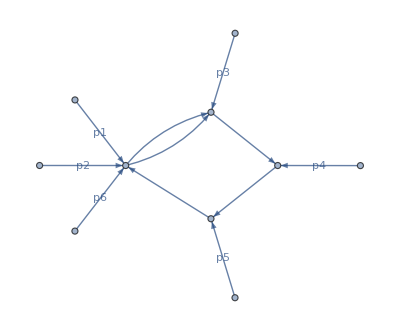
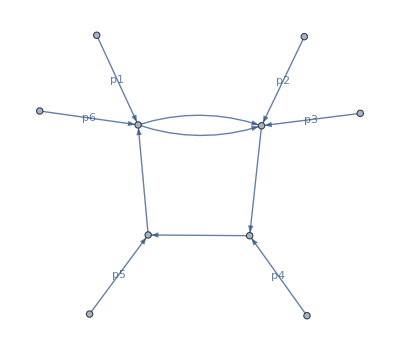
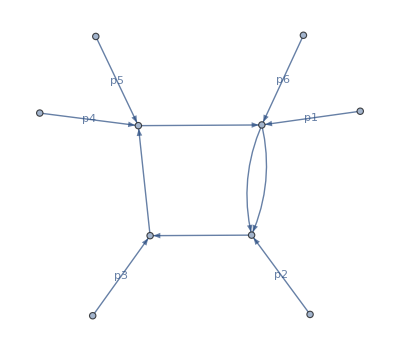
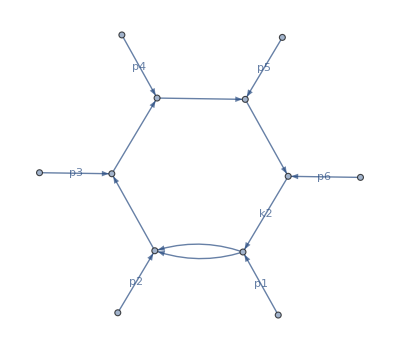
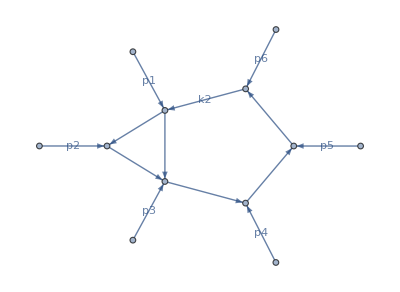
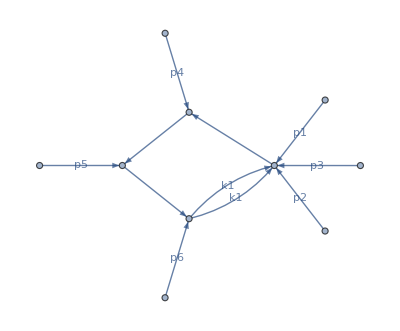
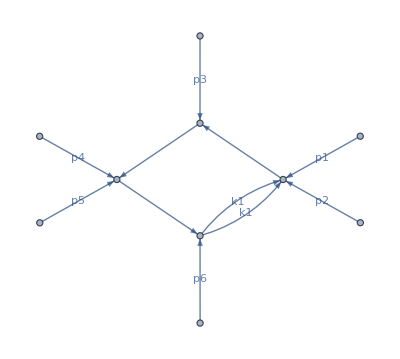
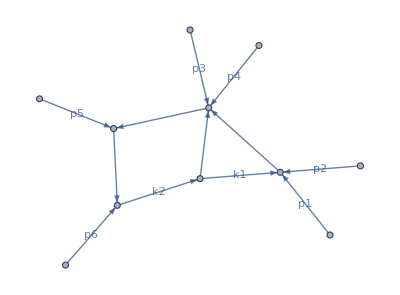
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-

```mathematica
PlotDiagrams=Table[plotDiagram[RemainingSectors[[i,1]]],{i,1,Length[RemainingSectors]}];
Grid[ArrayReshape[PlotDiagrams,{17,3}]]
```

```mathematica
17*3
```

51

```mathematica
RemSubBubbles={1,2,3,4,6,7,16,17,18,19,29,23,22,23,24,25,31,32,33};
ArrayReshape[RemainingSectors[[RemSubBubbles]][[All,2]],{4,5}]//MatrixForm
Grid[ArrayReshape[PlotDiagrams[[RemSubBubbles]],{4,5}]]
```

(1 | 1 | 1 | 1 | 1
1 | 2 | 2 | 2 | 2
2 | 2 | 2 | 2 | 2
2 | 2 | 2 | 2 | 0)

-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | 0

```mathematica
RemSubBubbles={1,2,3,4,6,7,16,17,18,19,29,23,22,23,24,25,31,32,33};
ArrayReshape[RemainingSectors[[RemSubBubbles]][[All,2]],{4,5}]//MatrixForm
Grid[ArrayReshape[PlotDiagrams[[RemSubBubbles]],{4,5}]]
```

```mathematica
Form=Thread[Total[Transpose[RemainingSectors[[RemSubBubbles]][[All,1]]]]]-1;
Permutation=FindPermutation[Form,Sort[Form]]
```

Cycles[{{1,3,5,6,7,8,9,12,14,15,16,17,2,4,19,18,11,13,10}}]

```mathematica
ResumBubbles2=Permute[RemSubBubbles,Permutation]
ArrayReshape[RemainingSectors[[ResumBubbles2]][[All,2]],{4,5}]//MatrixForm
Grid[ArrayReshape[PlotDiagrams[[ResumBubbles2]],{4,5}]]
```

{19,31,1,2,3,6,7,16,17,22,32,18,29,23,23,24,25,33,4}

(2 | 2 | 1 | 1 | 1
1 | 1 | 2 | 2 | 2
2 | 2 | 2 | 2 | 2
2 | 2 | 2 | 1 | 0)

-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | 0

```mathematica
RemainingSectors[[ResumBubbles2]][[1,1]]
RemainingSectors[[ResumBubbles2]][[2,1]]
```

{0,1,0,1,0,1,0,1,0,0,0,0,0}

{1,0,0,1,0,1,0,1,0,0,0,0,0}